```mathematica
Build[SetP[8],setp7]
```

Building poset setp7  ...

Done

```mathematica
BellB[8]
```

4140

```mathematica
Card[setp7]
```

877

```mathematica
setp7
```

setp7

```mathematica
Solve[ZetaPoly[setp7,n]==0,n]
```

Solve::fexp: Warning: Solve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{{n→0},{n→Root[-18+637 #1-3129 #1^2+6125 #1^3-5481 #1^4+1890 #1^5&,1]},{n→Root[-18+637 #1-3129 #1^2+6125 #1^3-5481 #1^4+1890 #1^5&,2]},{n→Root[-18+637 #1-3129 #1^2+6125 #1^3-5481 #1^4+1890 #1^5&,3]},{n→Root[-18+637 #1-3129 #1^2+6125 #1^3-5481 #1^4+1890 #1^5&,4]},{n→Root[-18+637 #1-3129 #1^2+6125 #1^3-5481 #1^4+1890 #1^5&,5]}}

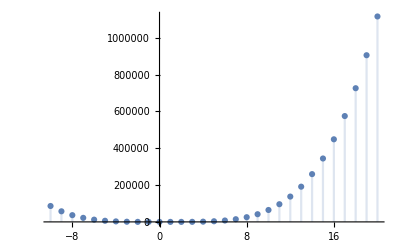

```mathematica
DiscretePlot[1/6 n (-4+30 n-65 n^2+45 n^3),{n,-10,20}]
```

```mathematica
MeetSubLattice[setp7]
```

MeetSubLattice[setp7]

```mathematica
Information[MeetSubLattice]
```

MeetSubLattice[name,S] returns the meet 
sublattice of P[name] generated by S. Both input and output
are sets of indices. Apply SubPoset next, then Build.

MeetSubLattice[Posets`Private`tag_,Posets`Private`points_]:=MeetSubLattice[Posets`Private`tag,Posets`Private`points]=FixedPoint[Posets`Private`fmeetsublattice[Posets`Private`tag,#1]&,Posets`Private`points]

```mathematica
P[setp7]
```

{{1,2,3,4,5,6,7},{1,1,3,4,5,6,7},{1,2,1,4,5,6,7},{1,2,3,1,5,6,7},{1,2,3,4,1,6,7},{1,2,3,4,5,1,7},{1,2,3,4,5,6,1},{1,2,2,4,5,6,7},{1,2,3,2,5,6,7},{1,2,3,4,2,6,7},{1,2,3,4,5,2,7},{1,2,3,4,5,6,2},{1,2,3,3,5,6,7},{1,2,3,4,3,6,7},{1,2,3,4,5,3,7},{1,2,3,4,5,6,3},{1,2,3,4,4,6,7},{1,2,3,4,5,4,7},{1,2,3,4,5,6,4},{1,2,3,4,5,5,7},838,{1,2,1,2,2,2,1},{1,2,1,2,2,2,2},{1,2,2,1,1,1,1},{1,2,2,1,1,1,2},{1,2,2,1,1,2,1},{1,2,2,1,1,2,2},{1,2,2,1,2,1,1},{1,2,2,1,2,1,2},{1,2,2,1,2,2,1},{1,2,2,1,2,2,2},{1,2,2,2,1,1,1},{1,2,2,2,1,1,2},{1,2,2,2,1,2,1},{1,2,2,2,1,2,2},{1,2,2,2,2,1,1},{1,2,2,2,2,1,2},{1,2,2,2,2,2,1},{1,2,2,2,2,2,2},{1,1,1,1,1,1,1}}
 |  |  |  |

```mathematica
g1=GraphFromSets[{{1,6},{2,7},{3,5},{4}}];
```

```mathematica
-Graphics-"13""♁""27""♁""4""♁""56"
```

```mathematica
g2=GraphFromSets[{{1,3},{2,7},{4},{5,6}}];
```

```mathematica
-Graphics-"14""♁""27""♁""3""♁""56",
```

```mathematica
g3=GraphFromSets[{{1,4},{2,7},{3},{5,6}}];
```

```mathematica
KnuthRep[{{1,3},{2,7},{4},{5,6}}]
```

{1,2,1,3,4,4,2}

```mathematica
KnuthRep[{{1,3},{2,7},{4},{5,6}}]
```

{1,2,1,3,4,4,2}

```mathematica
KnuthRep[{{1,4},{2,7},{3},{5,6}}]
```

{1,2,3,1,4,4,2}

```mathematica
knuall=P[setp7];
```

```mathematica
MemberQ[knuall,KnuthRep[{{1,3},{2,7},{4},{5,6}}]]
```

False

```mathematica
Length[knuall]
```

877

```mathematica
BellB[7]
```

877

```mathematica
KnuthRep2Sets[k_]:=Block[{result=Table[{},{i,Max[k]}]},
Table[result[[k[[i]]]]=Append[result[[k[[i]]]],i],{i,Length[k]}];
result
]
```

```mathematica
KnuthRep2Sets[{1,2,3,1,4,4,2}]
```

{{1,4},{2,7},{3},{5,6}}

```mathematica
Select[knuall,MemberQ[KnuthRep2Sets[#],{}]&]
```

{{1,1,3,4,5,6,7},{1,2,1,4,5,6,7},{1,2,3,1,5,6,7},{1,2,3,4,1,6,7},{1,2,3,4,5,1,7},{1,2,2,4,5,6,7},{1,2,3,2,5,6,7},{1,2,3,4,2,6,7},{1,2,3,4,5,2,7},{1,2,3,3,5,6,7},{1,2,3,4,3,6,7},{1,2,3,4,5,3,7},{1,2,3,4,4,6,7},{1,2,3,4,5,4,7},{1,2,3,4,5,5,7},{1,1,1,4,5,6,7},{1,1,3,1,5,6,7},{1,1,3,4,1,6,7},{1,1,3,4,5,1,7},{1,1,3,4,5,6,1},{1,1,3,3,5,6,7},{1,1,3,4,3,6,7},{1,1,3,4,5,3,7},{1,1,3,4,5,6,3},{1,1,3,4,4,6,7},{1,1,3,4,5,4,7},{1,1,3,4,5,6,4},{1,1,3,4,5,5,7},{1,1,3,4,5,6,5},{1,1,3,4,5,6,6},{1,2,1,1,5,6,7},{1,2,1,4,1,6,7},{1,2,1,4,5,1,7},{1,2,1,4,5,6,1},{1,2,1,2,5,6,7},{1,2,1,4,2,6,7},{1,2,1,4,5,2,7},{1,2,1,4,5,6,2},{1,2,1,4,4,6,7},{1,2,1,4,5,4,7},{1,2,1,4,5,6,4},{1,2,1,4,5,5,7},{1,2,1,4,5,6,5},{1,2,1,4,5,6,6},{1,2,3,1,1,6,7},{1,2,3,1,5,1,7},{1,2,3,1,5,6,1},{1,2,2,1,5,6,7},{1,2,3,1,2,6,7},{1,2,3,1,5,2,7},{1,2,3,1,5,6,2},{1,2,3,1,3,6,7},{1,2,3,1,5,3,7},{1,2,3,1,5,6,3},{1,2,3,1,5,5,7},{1,2,3,1,5,6,5},{1,2,3,1,5,6,6},{1,2,3,4,1,1,7},{1,2,3,4,1,6,1},{1,2,2,4,1,6,7},{1,2,3,2,1,6,7},{1,2,3,4,1,2,7},{1,2,3,4,1,6,2},{1,2,3,3,1,6,7},{1,2,3,4,1,3,7},{1,2,3,4,1,6,3},{1,2,3,4,1,4,7},{1,2,3,4,1,6,4},{1,2,3,4,1,6,6},{1,2,2,4,5,1,7},{1,2,3,2,5,1,7},{1,2,3,4,2,1,7},{1,2,3,3,5,1,7},{1,2,3,4,3,1,7},{1,2,3,4,4,1,7},{1,2,2,4,5,6,1},{1,2,3,2,5,6,1},{1,2,3,4,2,6,1},{1,2,3,3,5,6,1},{1,2,3,4,3,6,1},{1,2,3,4,4,6,1},{1,2,2,2,5,6,7},{1,2,2,4,2,6,7},{1,2,2,4,5,2,7},{1,2,2,4,5,6,2},{1,2,2,4,4,6,7},{1,2,2,4,5,4,7},{1,2,2,4,5,6,4},{1,2,2,4,5,5,7},{1,2,2,4,5,6,5},{1,2,2,4,5,6,6},{1,2,3,2,2,6,7},{1,2,3,2,5,2,7},{1,2,3,2,5,6,2},{1,2,3,2,3,6,7},{1,2,3,2,5,3,7},{1,2,3,2,5,6,3},{1,2,3,2,5,5,7},{1,2,3,2,5,6,5},{1,2,3,2,5,6,6},{1,2,3,4,2,2,7},{1,2,3,4,2,6,2},{1,2,3,3,2,6,7},{1,2,3,4,2,3,7},{1,2,3,4,2,6,3},{1,2,3,4,2,4,7},{1,2,3,4,2,6,4},{1,2,3,4,2,6,6},{1,2,3,3,5,2,7},{1,2,3,4,3,2,7},{1,2,3,4,4,2,7},{1,2,3,3,5,6,2},{1,2,3,4,3,6,2},{1,2,3,4,4,6,2},{1,2,3,3,3,6,7},{1,2,3,3,5,3,7},{1,2,3,3,5,6,3},{1,2,3,3,5,5,7},{1,2,3,3,5,6,5},{1,2,3,3,5,6,6},{1,2,3,4,3,3,7},{1,2,3,4,3,6,3},{1,2,3,4,3,4,7},{1,2,3,4,3,6,4},{1,2,3,4,3,6,6},{1,2,3,4,4,3,7},{1,2,3,4,4,6,3},{1,2,3,4,4,4,7},{1,2,3,4,4,6,4},{1,2,3,4,4,6,6},{1,1,1,1,5,6,7},{1,1,1,4,1,6,7},{1,1,1,4,5,1,7},{1,1,1,4,5,6,1},{1,1,1,4,4,6,7},{1,1,1,4,5,4,7},{1,1,1,4,5,6,4},{1,1,1,4,5,5,7},{1,1,1,4,5,6,5},{1,1,1,4,5,6,6},{1,1,3,1,1,6,7},{1,1,3,1,5,1,7},{1,1,3,1,5,6,1},{1,1,3,1,3,6,7},{1,1,3,1,5,3,7},{1,1,3,1,5,6,3},{1,1,3,1,5,5,7},{1,1,3,1,5,6,5},{1,1,3,1,5,6,6},{1,1,3,4,1,1,7},{1,1,3,4,1,6,1},{1,1,3,3,1,6,7},{1,1,3,4,1,3,7},{1,1,3,4,1,6,3},{1,1,3,4,1,4,7},{1,1,3,4,1,6,4},{1,1,3,4,1,6,6},{1,1,3,4,5,1,1},{1,1,3,3,5,1,7},{1,1,3,4,3,1,7},{1,1,3,4,5,1,3},{1,1,3,4,4,1,7},{1,1,3,4,5,1,4},{1,1,3,4,5,1,5},{1,1,3,3,5,6,1},{1,1,3,4,3,6,1},{1,1,3,4,5,3,1},{1,1,3,4,4,6,1},{1,1,3,4,5,4,1},{1,1,3,4,5,5,1},{1,1,3,3,3,6,7},{1,1,3,3,5,3,7},{1,1,3,3,5,6,3},{1,1,3,3,5,5,7},{1,1,3,3,5,6,5},{1,1,3,3,5,6,6},{1,1,3,4,3,3,7},{1,1,3,4,3,6,3},{1,1,3,4,3,4,7},{1,1,3,4,3,6,4},{1,1,3,4,3,6,6},{1,1,3,4,5,3,3},{1,1,3,4,4,3,7},{1,1,3,4,5,3,4},{1,1,3,4,5,3,5},{1,1,3,4,4,6,3},{1,1,3,4,5,4,3},{1,1,3,4,5,5,3},{1,1,3,4,4,4,7},{1,1,3,4,4,6,4},{1,1,3,4,4,6,6},{1,1,3,4,5,4,4},{1,1,3,4,5,4,5},{1,1,3,4,5,5,4},{1,1,3,4,5,5,5},{1,2,1,1,1,6,7},{1,2,1,1,5,1,7},{1,2,1,1,5,6,1},{1,2,1,1,2,6,7},{1,2,1,1,5,2,7},{1,2,1,1,5,6,2},{1,2,1,1,5,5,7},{1,2,1,1,5,6,5},{1,2,1,1,5,6,6},{1,2,1,4,1,1,7},{1,2,1,4,1,6,1},{1,2,1,2,1,6,7},{1,2,1,4,1,2,7},{1,2,1,4,1,6,2},{1,2,1,4,1,4,7},{1,2,1,4,1,6,4},{1,2,1,4,1,6,6},{1,2,1,4,5,1,1},{1,2,1,2,5,1,7},{1,2,1,4,2,1,7},{1,2,1,4,5,1,2},{1,2,1,4,4,1,7},{1,2,1,4,5,1,4},{1,2,1,4,5,1,5},{1,2,1,2,5,6,1},{1,2,1,4,2,6,1},{1,2,1,4,5,2,1},{1,2,1,4,4,6,1},{1,2,1,4,5,4,1},{1,2,1,4,5,5,1},{1,2,1,2,2,6,7},{1,2,1,2,5,2,7},{1,2,1,2,5,6,2},{1,2,1,2,5,5,7},{1,2,1,2,5,6,5},{1,2,1,2,5,6,6},{1,2,1,4,2,2,7},{1,2,1,4,2,6,2},{1,2,1,4,2,4,7},{1,2,1,4,2,6,4},{1,2,1,4,2,6,6},{1,2,1,4,5,2,2},{1,2,1,4,4,2,7},{1,2,1,4,5,2,4},{1,2,1,4,5,2,5},{1,2,1,4,4,6,2},{1,2,1,4,5,4,2},{1,2,1,4,5,5,2},{1,2,1,4,4,4,7},{1,2,1,4,4,6,4},{1,2,1,4,4,6,6},{1,2,1,4,5,4,4},{1,2,1,4,5,4,5},{1,2,1,4,5,5,4},{1,2,1,4,5,5,5},{1,2,3,1,1,1,7},{1,2,3,1,1,6,1},{1,2,2,1,1,6,7},{1,2,3,1,1,2,7},{1,2,3,1,1,6,2},{1,2,3,1,1,3,7},{1,2,3,1,1,6,3},{1,2,3,1,1,6,6},{1,2,3,1,5,1,1},{1,2,2,1,5,1,7},{1,2,3,1,2,1,7},{1,2,3,1,5,1,2},{1,2,3,1,3,1,7},{1,2,3,1,5,1,3},{1,2,3,1,5,1,5},{1,2,2,1,5,6,1},{1,2,3,1,2,6,1},{1,2,3,1,5,2,1},{1,2,3,1,3,6,1},{1,2,3,1,5,3,1},{1,2,3,1,5,5,1},{1,2,2,1,2,6,7},{1,2,2,1,5,2,7},{1,2,2,1,5,6,2},{1,2,2,1,5,5,7},{1,2,2,1,5,6,5},{1,2,2,1,5,6,6},{1,2,3,1,2,2,7},{1,2,3,1,2,6,2},{1,2,3,1,2,3,7},{1,2,3,1,2,6,3},{1,2,3,1,2,6,6},{1,2,3,1,5,2,2},{1,2,3,1,3,2,7},{1,2,3,1,5,2,3},{1,2,3,1,5,2,5},{1,2,3,1,3,6,2},{1,2,3,1,5,3,2},{1,2,3,1,5,5,2},{1,2,3,1,3,3,7},{1,2,3,1,3,6,3},{1,2,3,1,3,6,6},{1,2,3,1,5,3,3},{1,2,3,1,5,3,5},{1,2,3,1,5,5,3},{1,2,3,1,5,5,5},{1,2,2,4,1,1,7},{1,2,3,2,1,1,7},{1,2,3,3,1,1,7},{1,2,2,4,1,6,1},{1,2,3,2,1,6,1},{1,2,3,3,1,6,1},{1,2,2,2,1,6,7},{1,2,2,4,1,2,7},{1,2,2,4,1,6,2},{1,2,2,4,1,4,7},{1,2,2,4,1,6,4},{1,2,2,4,1,6,6},{1,2,3,2,1,2,7},{1,2,3,2,1,6,2},{1,2,3,2,1,3,7},{1,2,3,2,1,6,3},{1,2,3,2,1,6,6},{1,2,3,3,1,2,7},{1,2,3,3,1,6,2},{1,2,3,3,1,3,7},{1,2,3,3,1,6,3},{1,2,3,3,1,6,6},{1,2,2,4,5,1,1},{1,2,3,2,5,1,1},{1,2,3,3,5,1,1},{1,2,2,2,5,1,7},{1,2,2,4,2,1,7},{1,2,2,4,5,1,2},{1,2,2,4,4,1,7},{1,2,2,4,5,1,4},{1,2,2,4,5,1,5},{1,2,3,2,2,1,7},{1,2,3,2,5,1,2},{1,2,3,2,3,1,7},{1,2,3,2,5,1,3},{1,2,3,2,5,1,5},{1,2,3,3,2,1,7},{1,2,3,3,5,1,2},{1,2,3,3,3,1,7},{1,2,3,3,5,1,3},{1,2,3,3,5,1,5},{1,2,2,2,5,6,1},{1,2,2,4,2,6,1},{1,2,2,4,5,2,1},{1,2,2,4,4,6,1},{1,2,2,4,5,4,1},{1,2,2,4,5,5,1},{1,2,3,2,2,6,1},{1,2,3,2,5,2,1},{1,2,3,2,3,6,1},{1,2,3,2,5,3,1},{1,2,3,2,5,5,1},{1,2,3,3,2,6,1},{1,2,3,3,5,2,1},{1,2,3,3,3,6,1},{1,2,3,3,5,3,1},{1,2,3,3,5,5,1},{1,2,2,2,2,6,7},{1,2,2,2,5,2,7},{1,2,2,2,5,6,2},{1,2,2,2,5,5,7},{1,2,2,2,5,6,5},{1,2,2,2,5,6,6},{1,2,2,4,2,2,7},{1,2,2,4,2,6,2},{1,2,2,4,2,4,7},{1,2,2,4,2,6,4},{1,2,2,4,2,6,6},{1,2,2,4,5,2,2},{1,2,2,4,4,2,7},{1,2,2,4,5,2,4},{1,2,2,4,5,2,5},{1,2,2,4,4,6,2},{1,2,2,4,5,4,2},{1,2,2,4,5,5,2},{1,2,2,4,4,4,7},{1,2,2,4,4,6,4},{1,2,2,4,4,6,6},{1,2,2,4,5,4,4},{1,2,2,4,5,4,5},{1,2,2,4,5,5,4},{1,2,2,4,5,5,5},{1,2,3,2,2,2,7},{1,2,3,2,2,6,2},{1,2,3,2,2,3,7},{1,2,3,2,2,6,3},{1,2,3,2,2,6,6},{1,2,3,2,5,2,2},{1,2,3,2,3,2,7},{1,2,3,2,5,2,3},{1,2,3,2,5,2,5},{1,2,3,2,3,6,2},{1,2,3,2,5,3,2},{1,2,3,2,5,5,2},{1,2,3,2,3,3,7},{1,2,3,2,3,6,3},{1,2,3,2,3,6,6},{1,2,3,2,5,3,3},{1,2,3,2,5,3,5},{1,2,3,2,5,5,3},{1,2,3,2,5,5,5},{1,2,3,3,2,2,7},{1,2,3,3,2,6,2},{1,2,3,3,2,3,7},{1,2,3,3,2,6,3},{1,2,3,3,2,6,6},{1,2,3,3,5,2,2},{1,2,3,3,3,2,7},{1,2,3,3,5,2,3},{1,2,3,3,5,2,5},{1,2,3,3,3,6,2},{1,2,3,3,5,3,2},{1,2,3,3,5,5,2},{1,2,3,3,3,3,7},{1,2,3,3,3,6,3},{1,2,3,3,3,6,6},{1,2,3,3,5,3,3},{1,2,3,3,5,3,5},{1,2,3,3,5,5,3},{1,2,3,3,5,5,5},{1,1,1,1,1,6,7},{1,1,1,1,5,1,7},{1,1,1,1,5,6,1},{1,1,1,1,5,5,7},{1,1,1,1,5,6,5},{1,1,1,1,5,6,6},{1,1,1,4,1,1,7},{1,1,1,4,1,6,1},{1,1,1,4,1,4,7},{1,1,1,4,1,6,4},{1,1,1,4,1,6,6},{1,1,1,4,5,1,1},{1,1,1,4,4,1,7},{1,1,1,4,5,1,4},{1,1,1,4,5,1,5},{1,1,1,4,4,6,1},{1,1,1,4,5,4,1},{1,1,1,4,5,5,1},{1,1,1,4,4,4,7},{1,1,1,4,4,6,4},{1,1,1,4,4,6,6},{1,1,1,4,5,4,4},{1,1,1,4,5,4,5},{1,1,1,4,5,5,4},{1,1,1,4,5,5,5},{1,1,3,1,1,1,7},{1,1,3,1,1,6,1},{1,1,3,1,1,3,7},{1,1,3,1,1,6,3},{1,1,3,1,1,6,6},{1,1,3,1,5,1,1},{1,1,3,1,3,1,7},{1,1,3,1,5,1,3},{1,1,3,1,5,1,5},{1,1,3,1,3,6,1},{1,1,3,1,5,3,1},{1,1,3,1,5,5,1},{1,1,3,1,3,3,7},{1,1,3,1,3,6,3},{1,1,3,1,3,6,6},{1,1,3,1,5,3,3},{1,1,3,1,5,3,5},{1,1,3,1,5,5,3},{1,1,3,1,5,5,5},{1,1,3,4,1,1,1},{1,1,3,3,1,1,7},{1,1,3,4,1,1,3},{1,1,3,4,1,1,4},{1,1,3,3,1,6,1},{1,1,3,4,1,3,1},{1,1,3,4,1,4,1},{1,1,3,3,1,3,7},{1,1,3,3,1,6,3},{1,1,3,3,1,6,6},{1,1,3,4,1,3,3},{1,1,3,4,1,3,4},{1,1,3,4,1,4,3},{1,1,3,4,1,4,4},{1,1,3,3,5,1,1},{1,1,3,4,3,1,1},{1,1,3,4,4,1,1},{1,1,3,3,3,1,7},{1,1,3,3,5,1,3},{1,1,3,3,5,1,5},{1,1,3,4,3,1,3},{1,1,3,4,3,1,4},{1,1,3,4,4,1,3},{1,1,3,4,4,1,4},{1,1,3,3,3,6,1},{1,1,3,3,5,3,1},{1,1,3,3,5,5,1},{1,1,3,4,3,3,1},{1,1,3,4,3,4,1},{1,1,3,4,4,3,1},{1,1,3,4,4,4,1},{1,1,3,3,3,3,7},{1,1,3,3,3,6,3},{1,1,3,3,3,6,6},{1,1,3,3,5,3,3},{1,1,3,3,5,3,5},{1,1,3,3,5,5,3},{1,1,3,3,5,5,5},{1,1,3,4,3,3,3},{1,1,3,4,3,3,4},{1,1,3,4,3,4,3},{1,1,3,4,3,4,4},{1,1,3,4,4,3,3},{1,1,3,4,4,3,4},{1,1,3,4,4,4,3},{1,1,3,4,4,4,4},{1,2,1,1,1,1,7},{1,2,1,1,1,6,1},{1,2,1,1,1,2,7},{1,2,1,1,1,6,2},{1,2,1,1,1,6,6},{1,2,1,1,5,1,1},{1,2,1,1,2,1,7},{1,2,1,1,5,1,2},{1,2,1,1,5,1,5},{1,2,1,1,2,6,1},{1,2,1,1,5,2,1},{1,2,1,1,5,5,1},{1,2,1,1,2,2,7},{1,2,1,1,2,6,2},{1,2,1,1,2,6,6},{1,2,1,1,5,2,2},{1,2,1,1,5,2,5},{1,2,1,1,5,5,2},{1,2,1,1,5,5,5},{1,2,1,4,1,1,1},{1,2,1,2,1,1,7},{1,2,1,4,1,1,2},{1,2,1,4,1,1,4},{1,2,1,2,1,6,1},{1,2,1,4,1,2,1},{1,2,1,4,1,4,1},{1,2,1,2,1,2,7},{1,2,1,2,1,6,2},{1,2,1,2,1,6,6},{1,2,1,4,1,2,2},{1,2,1,4,1,2,4},{1,2,1,4,1,4,2},{1,2,1,4,1,4,4},{1,2,1,2,5,1,1},{1,2,1,4,2,1,1},{1,2,1,4,4,1,1},{1,2,1,2,2,1,7},{1,2,1,2,5,1,2},{1,2,1,2,5,1,5},{1,2,1,4,2,1,2},{1,2,1,4,2,1,4},{1,2,1,4,4,1,2},{1,2,1,4,4,1,4},{1,2,1,2,2,6,1},{1,2,1,2,5,2,1},{1,2,1,2,5,5,1},{1,2,1,4,2,2,1},{1,2,1,4,2,4,1},{1,2,1,4,4,2,1},{1,2,1,4,4,4,1},{1,2,1,2,2,2,7},{1,2,1,2,2,6,2},{1,2,1,2,2,6,6},{1,2,1,2,5,2,2},{1,2,1,2,5,2,5},{1,2,1,2,5,5,2},{1,2,1,2,5,5,5},{1,2,1,4,2,2,2},{1,2,1,4,2,2,4},{1,2,1,4,2,4,2},{1,2,1,4,2,4,4},{1,2,1,4,4,2,2},{1,2,1,4,4,2,4},{1,2,1,4,4,4,2},{1,2,1,4,4,4,4},{1,2,2,1,1,1,7},{1,2,2,1,1,6,1},{1,2,2,1,1,2,7},{1,2,2,1,1,6,2},{1,2,2,1,1,6,6},{1,2,2,1,5,1,1},{1,2,2,1,2,1,7},{1,2,2,1,5,1,2},{1,2,2,1,5,1,5},{1,2,2,1,2,6,1},{1,2,2,1,5,2,1},{1,2,2,1,5,5,1},{1,2,2,1,2,2,7},{1,2,2,1,2,6,2},{1,2,2,1,2,6,6},{1,2,2,1,5,2,2},{1,2,2,1,5,2,5},{1,2,2,1,5,5,2},{1,2,2,1,5,5,5},{1,2,2,4,1,1,1},{1,2,2,2,1,1,7},{1,2,2,4,1,1,2},{1,2,2,4,1,1,4},{1,2,2,2,1,6,1},{1,2,2,4,1,2,1},{1,2,2,4,1,4,1},{1,2,2,2,1,2,7},{1,2,2,2,1,6,2},{1,2,2,2,1,6,6},{1,2,2,4,1,2,2},{1,2,2,4,1,2,4},{1,2,2,4,1,4,2},{1,2,2,4,1,4,4},{1,2,2,2,5,1,1},{1,2,2,4,2,1,1},{1,2,2,4,4,1,1},{1,2,2,2,2,1,7},{1,2,2,2,5,1,2},{1,2,2,2,5,1,5},{1,2,2,4,2,1,2},{1,2,2,4,2,1,4},{1,2,2,4,4,1,2},{1,2,2,4,4,1,4},{1,2,2,2,2,6,1},{1,2,2,2,5,2,1},{1,2,2,2,5,5,1},{1,2,2,4,2,2,1},{1,2,2,4,2,4,1},{1,2,2,4,4,2,1},{1,2,2,4,4,4,1},{1,2,2,2,2,2,7},{1,2,2,2,2,6,2},{1,2,2,2,2,6,6},{1,2,2,2,5,2,2},{1,2,2,2,5,2,5},{1,2,2,2,5,5,2},{1,2,2,2,5,5,5},{1,2,2,4,2,2,2},{1,2,2,4,2,2,4},{1,2,2,4,2,4,2},{1,2,2,4,2,4,4},{1,2,2,4,4,2,2},{1,2,2,4,4,2,4},{1,2,2,4,4,4,2},{1,2,2,4,4,4,4},{1,1,1,1,1,1,7},{1,1,1,1,1,6,1},{1,1,1,1,1,6,6},{1,1,1,1,5,1,1},{1,1,1,1,5,1,5},{1,1,1,1,5,5,1},{1,1,1,1,5,5,5},{1,1,1,4,1,1,1},{1,1,1,4,1,1,4},{1,1,1,4,1,4,1},{1,1,1,4,1,4,4},{1,1,1,4,4,1,1},{1,1,1,4,4,1,4},{1,1,1,4,4,4,1},{1,1,1,4,4,4,4},{1,1,3,1,1,1,1},{1,1,3,1,1,1,3},{1,1,3,1,1,3,1},{1,1,3,1,1,3,3},{1,1,3,1,3,1,1},{1,1,3,1,3,1,3},{1,1,3,1,3,3,1},{1,1,3,1,3,3,3},{1,1,3,3,1,1,1},{1,1,3,3,1,1,3},{1,1,3,3,1,3,1},{1,1,3,3,1,3,3},{1,1,3,3,3,1,1},{1,1,3,3,3,1,3},{1,1,3,3,3,3,1},{1,1,3,3,3,3,3}}

```mathematica
Select[Map[KnuthRep2Sets,knuall],#[[1]]=={1,4}&]
```

{{{1,4},{2},{3},{},{5},{6},{7}},{{1,4},{2,3},{},{},{5},{6},{7}},{{1,4},{2,5},{3},{},{},{6},{7}},{{1,4},{2,6},{3},{},{5},{},{7}},{{1,4},{2,7},{3},{},{5},{6}},{{1,4},{2},{3,5},{},{},{6},{7}},{{1,4},{2},{3,6},{},{5},{},{7}},{{1,4},{2},{3,7},{},{5},{6}},{{1,4},{2},{3},{},{5,6},{},{7}},{{1,4},{2},{3},{},{5,7},{6}},{{1,4},{2},{3},{},{5},{6,7}},{{1,4},{2,3,5},{},{},{},{6},{7}},{{1,4},{2,3,6},{},{},{5},{},{7}},{{1,4},{2,3,7},{},{},{5},{6}},{{1,4},{2,3},{},{},{5,6},{},{7}},{{1,4},{2,3},{},{},{5,7},{6}},{{1,4},{2,3},{},{},{5},{6,7}},{{1,4},{2,5,6},{3},{},{},{},{7}},{{1,4},{2,5,7},{3},{},{},{6}},{{1,4},{2,5},{3,6},{},{},{},{7}},{{1,4},{2,5},{3,7},{},{},{6}},{{1,4},{2,5},{3},{},{},{6,7}},{{1,4},{2,6,7},{3},{},{5}},{{1,4},{2,6},{3,5},{},{},{},{7}},{{1,4},{2,6},{3,7},{},{5}},{{1,4},{2,6},{3},{},{5,7}},{{1,4},{2,7},{3,5},{},{},{6}},{{1,4},{2,7},{3,6},{},{5}},{{1,4},{2,7},{3},{},{5,6}},{{1,4},{2},{3,5,6},{},{},{},{7}},{{1,4},{2},{3,5,7},{},{},{6}},{{1,4},{2},{3,5},{},{},{6,7}},{{1,4},{2},{3,6,7},{},{5}},{{1,4},{2},{3,6},{},{5,7}},{{1,4},{2},{3,7},{},{5,6}},{{1,4},{2},{3},{},{5,6,7}},{{1,4},{2,3,5,6},{},{},{},{},{7}},{{1,4},{2,3,5,7},{},{},{},{6}},{{1,4},{2,3,5},{},{},{},{6,7}},{{1,4},{2,3,6,7},{},{},{5}},{{1,4},{2,3,6},{},{},{5,7}},{{1,4},{2,3,7},{},{},{5,6}},{{1,4},{2,3},{},{},{5,6,7}},{{1,4},{2,5,6,7},{3}},{{1,4},{2,5,6},{3,7}},{{1,4},{2,5,7},{3,6}},{{1,4},{2,5},{3,6,7}},{{1,4},{2,6,7},{3,5}},{{1,4},{2,6},{3,5,7}},{{1,4},{2,7},{3,5,6}},{{1,4},{2},{3,5,6,7}},{{1,4},{2,3,5,6,7}}}

```mathematica
Map[KnuthRep2Sets,knuall]
```

{{{1},{2},{3},{4},{5},{6},{7}},{{1,2},{},{3},{4},{5},{6},{7}},{{1,3},{2},{},{4},{5},{6},{7}},{{1,4},{2},{3},{},{5},{6},{7}},{{1,5},{2},{3},{4},{},{6},{7}},{{1,6},{2},{3},{4},{5},{},{7}},{{1,7},{2},{3},{4},{5},{6}},{{1},{2,3},{},{4},{5},{6},{7}},{{1},{2,4},{3},{},{5},{6},{7}},{{1},{2,5},{3},{4},{},{6},{7}},{{1},{2,6},{3},{4},{5},{},{7}},{{1},{2,7},{3},{4},{5},{6}},853,{{1,4,6},{2,3,5,7}},{{1,4,7},{2,3,5,6}},{{1,4},{2,3,5,6,7}},{{1,5,6,7},{2,3,4}},{{1,5,6},{2,3,4,7}},{{1,5,7},{2,3,4,6}},{{1,5},{2,3,4,6,7}},{{1,6,7},{2,3,4,5}},{{1,6},{2,3,4,5,7}},{{1,7},{2,3,4,5,6}},{{1},{2,3,4,5,6,7}},{{1,2,3,4,5,6,7}}}
 |  |  |  |

```mathematica
{{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}}}
```

{{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2}},{{1,2,3,1,4,4,2},{1,2,3,1,4,4,2}}}

```mathematica
MeetL[setp7,{1,2,3,4,5,4,7},{1,2,3,4,5,5,7}]
```

{1,2,3,4,5,6,7}

```mathematica
PointerNotation[p_]:=Block[{result=Table[{},{i,Length[Flatten[p]]}],block},
Table[
block=p[[i]];
Table[result[[el]]=Min[block],{el,block}]
,{i,Length[p]}
];
result
];
```

```mathematica
PointerNotation[]
```

```mathematica
PointerNotation[{{1,3},{2,7},{4},{5,6}}]
```

{1,2,1,4,5,5,2}

```mathematica
PointerNotation[{{1,4},{2,7},{3},{5,6}}]
```

{1,2,3,1,5,5,2}

```mathematica
MeetL[setp7,PointerNotation[{{1,3},{2,7},{4},{5,6}}],PointerNotation[{{1,4},{2,7},{3},{5,6}}]]
```

{1,2,3,4,5,5,2}

```mathematica
FromPointer[pointer_]:=Block[{result=Table[{},{i,Length[DeleteDuplicates[pointer]]}],map=Association[],k,c},
k=1;
Table[map[i]=k;k++,{i,Sort[DeleteDuplicates[pointer]]}];
Table[
c=map[pointer[[k]]];
result[[c]]=Append[result[[c]],k],{k,Length[pointer]}];
result
]
```

```mathematica
FromPointer[{1,2,3,1,5,5,2}]
```

{{1,4},{2,7},{3},{5,6}}

```mathematica
FromPointer[MeetL[setp7,PointerNotation[{{1,3},{2,7},{4},{5,6}}],PointerNotation[{{1,4},{2,7},{3},{5,6}}]]]
```

{{1},{2,7},{3},{4},{5,6}}

```mathematica
MyDistance[part1_,part2_]:=With[{m=FromPointer[MeetL[setp7,PointerNotation[part1],PointerNotation[part2]]]},
Length[m]-Length[part1]
]
```

```mathematica
MyDistance[{{1,3},{2,7},{4},{5,6}},{{1,4},{2,7},{3},{5,6}}]
```

{{1},{2,7},{3},{4},{5,6}}

1

```mathematica
$HistoryLength=10;
```